```mathematica
Integrate[Cos[x]^2,x]
```

x/2+1/4 Sin[2 x]

```mathematica
DSolve[D[y[x],{x,1}]==Cos[x]^2 Cos[2y[x]]^2,y[x],x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[x]→-1/2 ArcTan[1/4 (-4 x-C[1]-2 Sin[2 x])]},{y[x]→1/2 ArcTan[1/4 (4 x+C[1]+2 Sin[2 x])]}}

```mathematica
DSolve[{D[y[x],{x,1}]==(1-2x)y[x]^2,y[0]==-1/6},y[x],x]
```

{{y[x]→1/(-6-x+x^2)}}

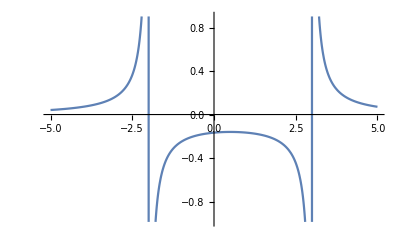

```mathematica
Plot[y[x]/.%6[[1]][[1]],{x,-5,5}]
```

```mathematica
Export["./figures/prob229.png",%11,ImageResolution->300]
```

./figures/prob229.png